```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll[point];
Options[point]={
	"n"->1,
	"s"->1
};
point[x_,{{dxL_,sL_,nL_},{dxR_,sR_,nR_}}]:=<|"x"->x,"dx"->{dxL,dxR},"s"->{sL,sR},"n"->{nL,nR}|>
point[x_,{dxL_,dxR_}]:=With[{s=OptionValue[point,"s"],n=OptionValue[point,"n"]},point[x,{{dxL,s,n},{dxR,s,n}}]]
point[x_,dx_]:=point[x,{dx,dx}]
point[x_,dx_,s_,n_]:=point[x,{{dx,s,n},{dx,s,n}}]
point[x_]:=point[x,{{0,0,0},{0,0,0}}]

draw`point[point_Association]:=Module[{pi,i},
	If[point["n"]==={0,0}, (* Single point*)
		Return[{point["x"]}];
	];
	
	pi={};
	Block[{x=point["x"],n=First@point["n"],d=First@point["dx"],s=First@point["s"],si,dxv},
		If[n>0,
			si=s/n;
			dxv=Normalize[x-{First[x]+1,Last[x]+d}];
			pi=pi~Join~Table[x+dxv*si*i,{i,1,n}];
		];
	];
	pi=pi~Join~{point["x"]};
	Block[{x=point["x"],n=Last@point["n"],d=Last@point["dx"],s=Last@point["s"],si,dxv},
		If[n>0,
			si=s/n;
			dxv=Normalize[{First[x]+1,Last[x]+d}-x];
			pi=pi~Join~Table[x+dxv*si*i,{i,1,n}];
		];
	];
	pi
]
draw`point[l_List]:=Flatten[draw`point[#]&/@l,1];
```

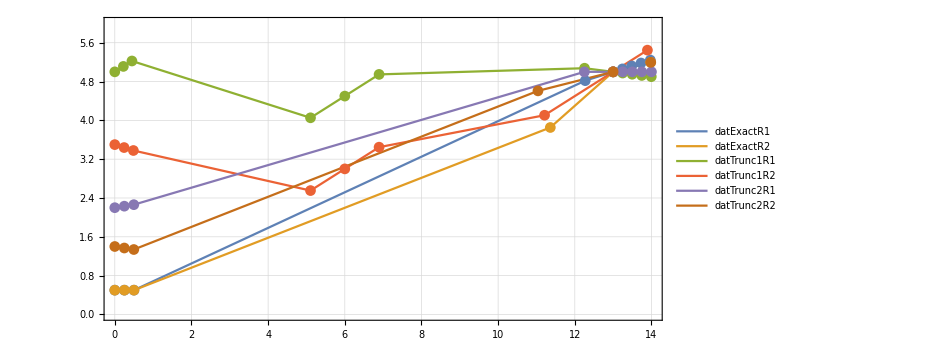

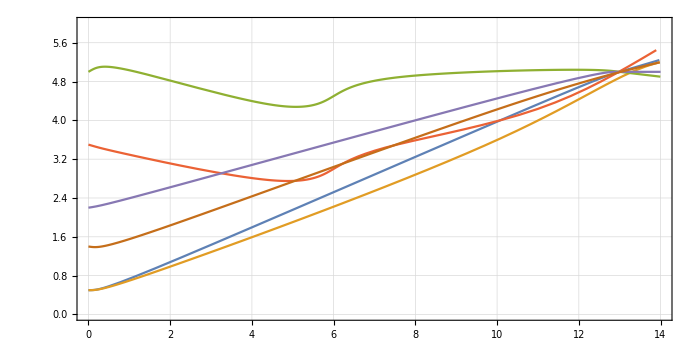

```mathematica
Options[point]={"n"->1,"s"->1};
kUV=13;
kIR=0;

ΓIR=point[{kIR,0.5},{{0,0,0},{0,0.5,2}}];

datExactR1=draw`point@{ΓIR,point[{kUV,5},{{0.25,0.75,1},{0.25,1,4}}]};
datExactR2=draw`point@{ΓIR,point[{kUV,5},{{.7,2,1},{0.2,1,1}}]};

datTrunc1R1=draw`point@{point[{kIR,5},{{0,0,0},{0.5,0.5,2}}],point[{6,4.5},{{0.5,1,1},{0.5,1,1}}],point[{kUV,5},{{-0.1,0.75,1},{-0.1,1,4}}]};
datTrunc1R2=draw`point@{point[{kIR,3.5},{{0,0,0},{-0.25,0.5,2}}],
point[{6,3},{{0.5,1,1},{0.5,1,1}}],point[{kUV,5},{{.5,2,1},{0.5,1,1}}]};

datTrunc2R1=draw`point@{point[{kIR,2.2},{{0,0,0},{0.125,0.5,2}}],point[{kUV,5},{{0.,0.75,1},{0.,1,4}}]};
datTrunc2R2=draw`point@{point[{kIR,1.4},{{0,0,0},{-0.125,0.5,2}}],point[{kUV,5},{{0.2,2,1},{0.2,1,1}}]};

dat=Association[#->N@ToExpression[#]&/@{"datExactR1","datExactR2","datTrunc1R1","datTrunc1R2","datTrunc2R1","datTrunc2R2"}];

opts=Sequence@@{PlotRange->{{0,14},{0,6}},AspectRatio->1/2,GridLines->Automatic,Frame->True,ImageSize->50*{14,6}};
ListPlot[dat,Joined->True,Mesh->All,opts]

BSplineFunction/@Values@dat;
#[t]&/@%;
Show[{ParametricPlot[%,{t,0,1}]},opts]

AssociateTo[dat,<|"kUV"->kUV,"kIR"->kIR,"data"->{"datExactR1","datExactR2","datTrunc1R1","datTrunc1R2","datTrunc2R1","datTrunc2R2"},"labels"->{"$R_1, e$","$R_2, e$","$R_1, t_1$","$R_2, t_1$","$R_1, t_2$","$R_2, t_2$"}|>];
Export["truncation.json",%];
```

```mathematica
ΓLpT=point[{kLp,4.25},-0.2];

ΓIRT0=point[{kIR,1},{{0,0,0},{0,0.5,2}}];
ΓIRT=point[{kIR,3},{{0,0,0},{0,0.5,2}}];
ΓIRTwrong=point[{kIR,3.5},{{0,0,0},{0,0.5,2}}];

datT0=draw`point@{ΓIRT0,ΓLpT0,ΓUVT0};
datT=draw`point@{ΓIRT,point[{4,2.5}],ΓLpT,ΓUVT0};
```